# L/M-Plots: GR-Completeness

“Nachbau” der Plots, die in NS2012 drin sind.

### Helpers

```mathematica
(* helpers: *)
square[{x_,y_},rad_] := Rectangle[{x-rad,y-rad},{x+rad,y+rad}]
SetDirectory[NotebookDirectory[]];
cm=72/2.54;
(* Labels direkt auf Funktionen anzeigen *)
ClearAll[EpiLabels]
(* Fuer Funktionen von Listen *)
EpiLabels[xpoint_,data_, labels_, axisratio_:1]:= (* labels and data must have same dimension *)
With[{xpoints=If[Head@xpoint===List, xpoint, xpoint&/@ labels]}, (* erlaube Liste von xpoints *)
Text[
Rotate[labels⟦n⟧,ArcTan[ data'[xpoints⟦n⟧]⟦n⟧ / axisratio](*, {Left,Bottom} *)],
{xpoints⟦n⟧, 0 + data[xpoints⟦n⟧]⟦n⟧},
Background -> White
(* Opacity[0.8,White]*)
] ~Table~{n, Range@Length@labels}]
(* Fuer Listen von Funktionen *)
EpiLabelsLoF[xpoint_,data_, labels_, axisratio_:1]:= (* labels and data must have same dimension *)
With[{xpoints=If[Head@xpoint===List, xpoint, xpoint&/@ labels]}, (* erlaube Liste von xpoints *)
Text[
Rotate[labels⟦n⟧,ArcTan[ data⟦n⟧'[xpoints⟦n⟧] / axisratio](*, {Left,Bottom} *)],
{xpoints⟦n⟧, 0 + data⟦n⟧[xpoints⟦n⟧]},
Background -> White
(* Opacity[0.8,White]*)
] ~Table~{n, Range@Length@labels}]
(* Mal testen, Rotate und Text zu vertauschen (einfach "rt" hintendran): *)
EpiLabelsLoFrt[xpoint_,data_, labels_, axisratio_:1]:= 
With[{xpoints=If[Head@xpoint===List, xpoint, xpoint&/@ labels]},
Inset[
Rotate[
Text[labels⟦n⟧,Background-> White],
ArcTan[ data⟦n⟧'[xpoints⟦n⟧] / axisratio](*, {Left,Bottom} *)
],
{xpoints⟦n⟧, 0 + data⟦n⟧[xpoints⟦n⟧]}
(* Opacity[0.8,White]*)
] ~Table~{n, Range@Length@labels}]
```

```mathematica
(* Numerische Inversion mithilfe einer adaptiv erstellten Wertetabelle *)
Ninv[f_,{Xmin_,Xmax_}] :=Module[{data},
(* Erzeuge adaptive Wertetabelle *)
data=Reap[Plot[f[x],{x,Xmin,Xmax},EvaluationMonitor:>Sow@{x,f[x]}]]⟦-1,1⟧;
(* Sortiere sie nach steigenenden x-Werten *)
data = Sort[data,#1⟦1⟧ < #2⟦1⟧ &];
(* Invertiere Wertetabelle *)
data⟦All, {1,2}⟧ = data⟦All, {2,1}⟧;
(* Das Ergebnis ist eine Wertetabelle {x,f[x]} im gewuenschten Range *)
data
]
(* Loesche ungewuenschte Werte raus *)
Ninv[f_,{Xmin_, Xmax_},{Ymin_,Ymax_}] := Select[Ninv[f,{Xmin,Xmax}],
Ymin ≤ #⟦1⟧ ≤ Ymax &]
```

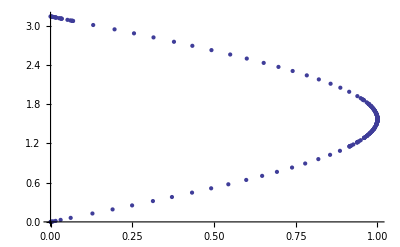

```mathematica
ListPlot[Ninv[Sin,{0,π}]]
```

## Die Schwarzschild BH-Teilchen-Dualität

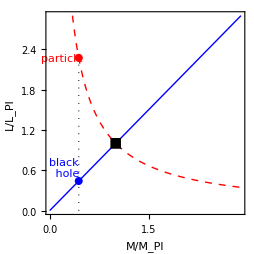

```mathematica
basic = Plot[Evaluate@{
1/x,x},
{x,0,3-0.1},PlotRange-> {0,3-0.1},
Frame-> True,
AspectRatio->1,
PlotRangePadding->None,
(*FrameTicks-> ({{{1,#},{2,""},{3,""}},None}&/@ {"L_P","M_P"}),*)
PlotStyle -> {
{Dashed, Red},
{Blue}
},
Epilog-> {
Black,square[{1,1},.08]
}~Join~Block[{
M=0.44,
par = {M, 1/M}, (* particle position *)
bh = {M,M} (* bh position *)
},{
(* Duality: *)
Dotted, Black,Line@{{M, 0},par},
Red, Disk[par,.06],
Text["particle", par-{.25,0}],
Blue, Disk[bh,.06],
Text["black \n hole", bh-{.2,-.2}],
}],
FrameLabel-> {"M/M_Pl", "L/L_Pl"},(*
PlotLabel-> "Schwarzschild",*)
ImageSize-> 9cm
]
```

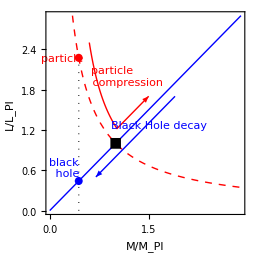

```mathematica
(* build arrow indicators *)
particleArrow=
Plot[Block[
(* Offset von Originalkurve durch X-Offset berechnen.
  Die neue Schnittstelle ist gegeben durch Solve[1/(x-a)==(x+a), x] *)
{off=0.2,yL=x-off, yR=x+off},
If[x≤ √(1+off^2),1/yL, yR]], {x,0.6,1.5},
PlotStyle-> {Thick, Red}
] /. Line[x__]:> Sequence[Arrowheads[.06],Arrow[x]];
bhArrow=Plot[(x-0.2), {x,0.7,1.9},
PlotStyle-> {Thick, Blue}
] /. Line[x__]:> Sequence[Arrowheads[{-.06,0}],Arrow[x]];
simpleSMM=Show[basic,particleArrow,bhArrow,Graphics@{
Red,Text["particle\n         compression",{0.95,2.0}],
Blue,Text["Black Hole decay",{1.65,1.28}]~Rotate~(45°)
}]
```

```mathematica
Export["../figures/completeness-schwarzschild.pdf", simpleSMM]
```

../figures/completeness-schwarzschild.pdf

## BH-Teilchendualität im ADD-Szenario (Schwarzschild-Tangherlini)

Hier ist alles irgendwie ziemlich anders: Die Masse skaliert bei H(r)=1 mit
M/M* = (n+2)  (r_H/L*)^(n+1), also quadratisch, usw.:

```mathematica
(* SSL = Schwarzschild-Laenge, also Ereignishorizont *)
SSL[M_, n_] = (M/(1 (*n+2*)))^(1/(n+1))
```

M^(1/(1+n))

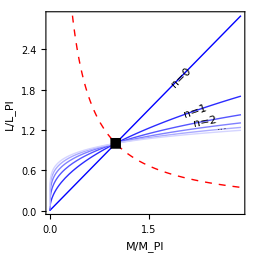

```mathematica
nChoices = Range[0,5];
STMfigure = Plot[Evaluate@Join[
{1/M},
Table[SSL[M,n],{n,nChoices}]
],
{M,0,3-0.1},
PlotRange-> {0,3-0.1},
Frame-> True,
AspectRatio->1,
PlotRangePadding->None,
(*FrameTicks-> ({{{1,#},{2,""},{3,""}},None}&/@ {"L_P","M_P"}),*)
PlotStyle -> Join[
{{Dashed, Red}},
Table[{Blend[{Blue,White},n/Length@nChoices]},{n,nChoices}] 
],
Epilog-> {
Black,square[{1,1},.08],
EpiLabels[{2.0, 2.2,2.35,2.61},Function[M,Table[SSL[M,n],{n,nChoices}]],  {"n=0","n=1","n=2", "..."}]
},
FrameLabel-> {"M/M_Pl", "L/L_Pl"},
ImageSize-> 9cm
]
```

```mathematica
Export["../figures/completeness-STM.pdf", STMfigure]
```

../figures/completeness-STM.pdf

## GR Self-Completeness durch Holographie-Metrik

```mathematica
h[r_,n_:0] = r^(2+n) / (r^(2+n)+1)
r0[n_] = (1+n)^(-1/(2+n)) (* ACHTUNG bei Definition von r0! *)
```

r^(2+n)/(1+r^(2+n))

(1+n)^(-1/(2+n))

### Holographie in 1d

```mathematica
InverseFunction[1/2 (#^2 + 1) / #&]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

#1-√(-1+#1^2)&

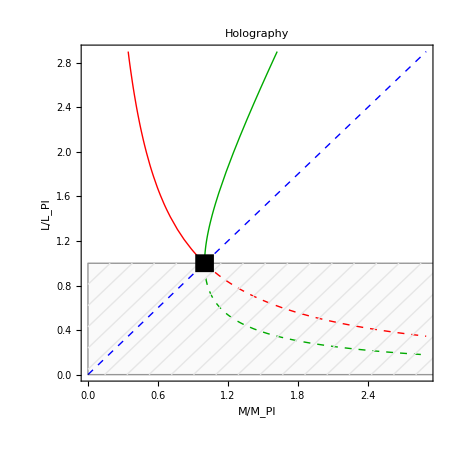

```mathematica
shading = RegionPlot[ x ≤ 1, {y,0,3},{x,0,3},
Mesh->20,MeshFunctions->{#1-#2&},MeshShading->{None},
MeshStyle-> GrayLevel[0.9]];
holo=Plot[ Evaluate[{
M+√(M^2-1), M-√(M^2-1),
If[M≤ 1,1/M,],If[M≥ 1,1/M,],
If[M≥ 1, M, ],If[M≤ 1, M, ]
}],
{M,0,3-0.1},PlotRange-> {0,3-0.1},
Frame-> True,
PlotStyle -> {
{Thick,Darker@Green},{Thick, Dashed, Darker@Green},
{Red},{Dashed, Red},
{Dashed,Blue}, {Dashed,Blue}
},
AspectRatio->1,
PlotRangePadding->None,
Prolog-> {
GrayLevel[.98],Rectangle[{0,0},{3,1}]
},
Epilog-> {
Black,square[{1,1},.08]
},
FrameLabel-> {"M/M_Pl", "L/L_Pl"},
PlotLabel-> "Holography"
]~Show~shading
```

```mathematica
(*GraphicsGrid[{{simpleSMM,holo}}]*)
```

### Holographie in n dim

```mathematica
M[r_,n_, H_]=(n+2) r^(n+1) / H[r,n]
```

((2+n) r^(1+n))/H[r,n]

```mathematica
M[r,2,h]
```

(4 (1+r^4))/r

Die analytische Inverse ist bei n=0 “gerade noch” kontrollierbar, da man den negativen Wurzelbranch einfach manuell hinzufügen kann. Bei n>0 ist das nicht mehr so direkt sichtbar und die Ausdrücke werden zumindest in Mathematica beliebig schwierig. Da wir nur eine Plottingauflösung brauchen, verwenden wir daher numerische Invertierung.

```mathematica
With[{n=1},InverseFunction[1/(2+n) (#^(2+n) + 1) / #^(1+n)&]]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

#1+(2^(1/3) #1^2)/((-1+2 #1^3+√(1-4 #1^3))^(1/3))+((-1+2 #1^3+√(1-4 #1^3))^(1/3))/2^(1/3)&

Was ich im folgenden zeigen will, ist ein Plot, wo r auf r0 und M auf M(r0) normiert ist. Das entspricht der Längenskala auf L_* und der Massenskala auf M_* normiert. Hier schonmal die Normierung der Längenskala:

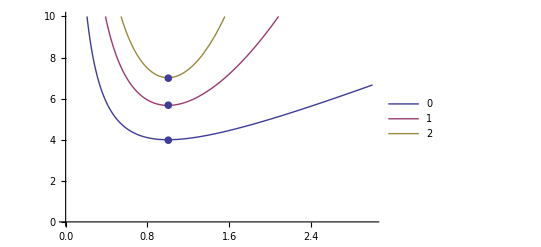

```mathematica
Show[
Plot[Evaluate[ M[r r0[n],n,h]~Table~{n,0,2}],{r,0,3}, PlotRange-> {0,10},PlotLegends-> {0,1,2}],
ListPlot[ Table[ {1, M[r0[n],n,h]}, {n,0,2}], PlotMarkers->{Automatic,10}]
]
```

Und hier auch der Massenskala:

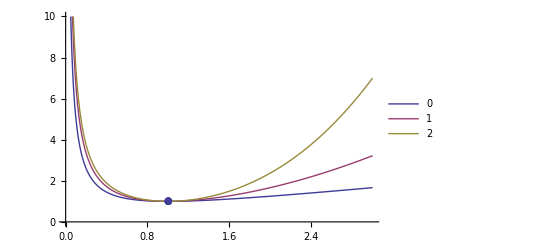

```mathematica
Show[
Plot[Evaluate[ (M[r r0[n],n,h]/M[r0[n],n,h])~Table~{n,0,2}],{r,0,3}, PlotRange-> {0,10},PlotLegends-> {0,1,2}],
ListPlot[ Table[ {1,1}, {n,0,2}], PlotMarkers->{Automatic,10}]
]
```

Dieses Bild wird nun aufwändig um 90° gekippt, indem die Umkehrfunktion gebidlet wird:

```mathematica
(* Shorthands to cut branches out of the double valued functions *)
upperBranch[data_] := Select[data,#⟦2⟧>1&];
lowerBranch[data_] := Select[data,#⟦2⟧<1&];
```

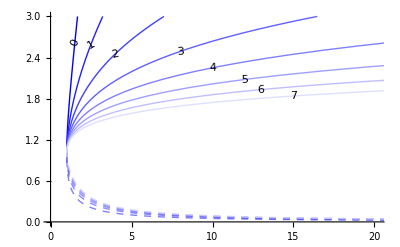

```mathematica
(* Einfache Moeglichkeit, die Ninv zu plotten: Listlineplot *)
nFigHolo=Block[{nChoices=Range[0,7]},
(* data kann man jetzt direkt plotten *)
data= Table[Ninv[ M[# r0[n],n,h]/ M[r0[n],n,h] &,{0,3},{0,70}],{n,nChoices}];
(* Um die Labels zu machen, muss man den Umweg ueber nichtnumerische Funktionen gehen: *)
labely = Interpolation[upperBranch@#,InterpolationOrder->1]&/@ data;
Off[InterpolatingFunction::dmval]; (* bloede Interpolation *)
ListLinePlot[ 
Flatten[{upperBranch@#,lowerBranch@#}&/@ data, 1] /. { {}-> {{0,0}} },
PlotStyle-> Transpose@{
Table[{Blend[{Blue,White},n/Length@nChoices]},{n,nChoices}],
Table[{Opacity[.5],Dashed,Blend[{Blue,White}, n/Length@nChoices]},{n,nChoices}]
}~Flatten~1,
InterpolationOrder->1,
Epilog-> {
EpiLabelsLoF[{1.5,2.5,4, 8,10,12,13,15},labely,  nChoices]
}
]]
```

Einbettung in die L-M-Figur. Es gibt zwei Varianten: Den ListLinePlot per Show mit dem Grundplot zusammenzufügen, oder den ganzen Plot auf einmal zu machen und die Liste dabei linear zu interpolieren (das macht ListLinePlot letztlich auch intern: Interpolieren und dann wieder abtasten)). Ich wähle hier den letzteren Weg, um die Epilabels einfacher anbringen zu können.

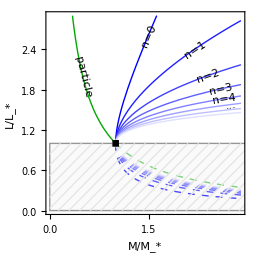

```mathematica
holoN = Range[0,7];
nChoices = Range[0,7];
holoDataN= Table[Ninv[ M[# r0[n],n,h]/ M[r0[n],n,h] &,{0,3},{0,70}],{n,nChoices}];
holoUpper = Interpolation[upperBranch@#,InterpolationOrder->1]&/@ holoDataN;
holoLower = Interpolation[lowerBranch@#,InterpolationOrder->1]&/@ holoDataN;
holoN = Show[Plot[ Evaluate@Join[{
If[M≤ 1,1/M,],If[M≥ 1,1/M,]
(*,If[M≥ 1, M, ],If[M≤ 1, M, ] *)
}, 
If[M≥ 1, #[M],]&/@holoUpper,
If[M≥ 1, #[M],]&/@holoLower],
{M,0,3-0.1},PlotRange-> {0,3-0.1},
Frame-> True,
PlotStyle -> Join[{
{Thick,Darker@Green},{Thick, Opacity[.5],Dashed, Darker@Green}
},
Table[{Blend[{Blue,White},n/Length@nChoices]},{n,nChoices}],
Table[{Opacity[.7],Dashed,Blend[{Blue,White}, n/Length@nChoices]},{n,nChoices}]
],
AspectRatio->1,
ImageSize-> 9cm,
PlotRangePadding->None,
Prolog-> {
GrayLevel[.98],Rectangle[{0,0},{3,1}]
},
Epilog-> {
Black,square[{1,1},.05],
EpiLabelsLoFrt[{0.5}, {1/#&}, {"particle"}],
EpiLabelsLoFrt[{1.5,2.2,2.4, 2.6,2.65,2.75},holoUpper,  {"n=0","n=1","n=2","n=3","n=4","..."}]
},
FrameLabel-> {"M/M_*", "L/L_*"}
(*,PlotLabel-> "Holography in ndims"*)
],
shading
(* Hier hätte man elegant die nFigHolo einblenden koennen, kriegt
aber dann Probleme mit den Epilabels. *)
(*nFigHolo*)]
```

```mathematica
Export["../figures/completeness-holoN.pdf", holoN]
```

../figures/completeness-holoN.pdf

## GR Self-Completeness durch Self-regular

Hier der gleiche Plot wie bei der Holographie, nur

```mathematica
ClearAll[a] (* ha keine Func von a wg def von M *)
ha[r_,n_:0] = r^(3+n) / (r^a+1/2)^((3+n)/a)
r0a[n_,a_] = (1+n)^(-1/a) (* ACHTUNG bei Definition von r0! *)
a0 = 3/Log[2] * Log[3/2];
MassA[r_,aa_,nn_:0] = M[r  r0a[nn,aa],nn,ha] / M[r0a[nn,aa],nn,ha] /. {a-> aa}
```

r^(3+n) (1/2+r^a)^(-(3+n)/a)

(1+n)^(-1/a)

((1/2+((1+nn)^(-1/aa))^aa)^(-(3+nn)/aa) (1/2+((1+nn)^(-1/aa) r)^aa)^((3+nn)/aa))/r^2

```mathematica
Solve[MassA[r,aa]==y, aa]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[((2/3)^(3/aa) (1/2+r^aa)^(3/aa))/r^2==y,aa]

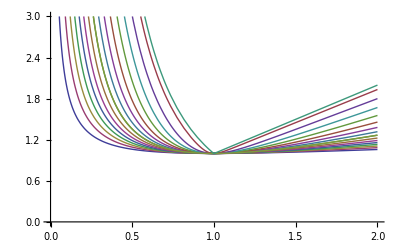

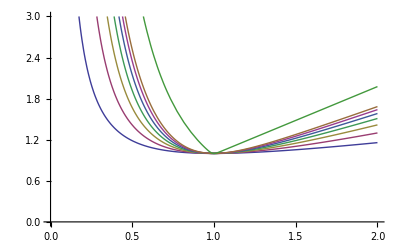

```mathematica
Plot[Evaluate@MassA[r,aChoices],{r,0,2},PlotRange-> {0,3}]
```

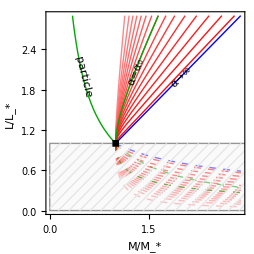

```mathematica
(* hier entnommen der Analysen von h-profiles.nb *)
equalAlphasFromHPROFILES ={0.5182294525691176,0.8289394440115383,1.0811589400635773,1.3389395734927274,1.6225936131657517,1.9487080693304009,2.33697315715288,2.8150423708910237,3.4257244741705515,4.240949185273588,5.393167150699948,7.157435517449798,10.215751830541969,16.854187061344945,42.42095375538363};
equalAlphaseFromRemnantPlots = {0.3577210902210111,0.5282900919157304,0.6788853002488767,0.835845626502327,1.0103177634782203,1.2123916507499746,1.454586716687683,1.754887447510871,2.1416011658365552,2.6631043642868013,3.410375005267028,4.5780234291746496,6.6717032485736665,11.545077552532236,35.85349777305797};
equalAlphas = equalAlphaseFromRemnantPlots;
aChoices = equalAlphas~Join~{a0,1000} (*{1,2,3,4,5,6,7,100};*);
hAdata = Table[Ninv[ MassA[#,aa]&, {0,3},{0,100}],{aa,aChoices}];
(* Lower and upper interpolation functions *)
{hAupper,hAlower} = Function[dataA,Interpolation[#@dataA,InterpolationOrder->1]]/@ hAdata& /@ {upperBranch,lowerBranch};
hAfig = Show[Plot[ Evaluate@Join[{If[M≤ 1,1/M,],If[M≥ 1,1/M,]}, 
If[M≥ 1, #[M],]&/@hAupper, If[M≥ 1, #[M],]&/@hAlower],
{M,0,3-0.1},PlotRange-> {0,3-0.1},
Frame-> True,
PlotStyle -> Join[{
{Thick,Darker@Green},{Thick, Opacity[.5],Dashed, Darker@Green}
},
Lighter[Red, 0.6*Rescale[#,{0,Length@aChoices}]]&/@Reverse@Range@Length@equalAlphas,
{{Thick,Darker@Green},{Thick, Blue}},
{Opacity[.5], Dashed, Lighter[Red, 0.6*Rescale[#,{0,Length@aChoices}]]}&/@Reverse@Range@Length@equalAlphas,
{{Opacity[.5],Dashed,Thick,Darker@Green},{Opacity[.5],Dashed,Thick, Blue}}
(*Table[{Opacity[.5],Dashed,Blend[{Blue,White}, n/Length@nChoices]},{n,aChoices}]*)
],
AspectRatio->1,
ImageSize-> 9cm,
PlotRangePadding->None,
Prolog-> {
GrayLevel[.98],Rectangle[{0,0},{3,1}]
},
Epilog-> {
Black,square[{1,1},.05],
EpiLabelsLoFrt[{0.5}, {1/#&}, {"particle"}],
EpiLabelsLoFrt[{2},{hAupper⟦-1⟧},  {"α→∞"}],
EpiLabelsLoFrt[{1.3},{hAupper⟦-2⟧},  {"α=α_0"}]
},
FrameLabel-> {"M/M_*", "L/L_*"}
],
shading]
```

```mathematica
Export["../figures/completeness-halpha.pdf", hAfig]
```

../figures/completeness-halpha.pdf

## Vergleich mit GUP

Dieser Bereich wurde von Calc14, Kempf2005-Plot.nb kopiert/übernommen.

```mathematica
xB[p_,β_,γ_] = (1+p^2 β+γ)/(2 p);
MinimumP[β_,γ_]=(√(1+γ))/(√β);
MinimumX[β_,γ_] = xB[MinimumP[β,γ],β,γ];
```

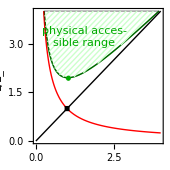

```mathematica
gup  = With[{β=1.9,γ=1, xymax=4},
shading = RegionPlot[y≥ xB[M,β,γ], {M,0,xymax},{y,0,xymax},
Mesh->20,MeshFunctions->{#1-#2&},MeshShading->{None},
MeshStyle->Lighter[Green,0.8]];
Plot[ Evaluate[{
xB[M,β,γ],
If[M≤ 1,1/M,],If[M≥ 1,1/M,],
If[M≥ 1, M, ],If[M≤ 1, M, ]
}],
{M,0,xymax},
PlotRange-> {0,xymax},
Frame-> True,
ImageSize-> 6cm,
PlotStyle -> {
{Thick,Darker@Green},
{Red},{Red},
{Black},{Black}
},
AspectRatio->1,
PlotRangePadding->None,
Epilog-> {
Black,square[{1,1},.08],
Darker@Green, Disk[{MinimumP[β,γ],MinimumX[β,γ]},0.08],
Darker@Green, Text["physical acces-\nsible range", {1.55,3.2}]
},
FrameLabel->  {"M/M_*", "L/L_*"}(*,
PlotLabel-> "GUP"*)
]~Show~shading]
```

```mathematica
Export["../figures/completeness-simple-gup.pdf", gup(*, ImageSize-> 8cm*)]
```

../figures/completeness-simple-gup.pdf

### Vergleichssachen für Nicolini (GUP vs Holo), alt

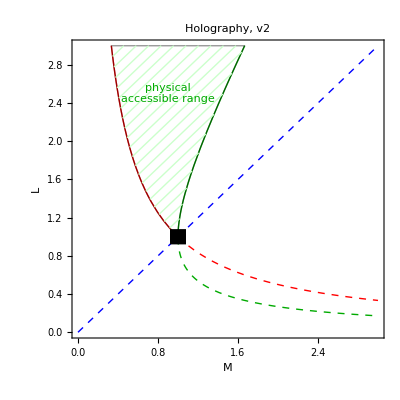

```mathematica
holo2 =With[{xymax=3},
shading = RegionPlot[ 
y ≥ If[M≥ 1, M+√(M^2-1), 1/M], {M,0,xymax},{y,0,xymax},
Mesh->20,MeshFunctions->{#1-#2&},MeshShading->{None},
MeshStyle->  Lighter[Green,0.8]];
 Plot[ Evaluate[{
M+√(M^2-1), M-√(M^2-1),
If[M≤ 1,1/M,],If[M≥ 1,1/M,],
If[M≥ 1, M, ],If[M≤ 1, M, ]
}],
{M,0,xymax},
PlotRange-> {0,xymax},
Frame-> True,
PlotStyle -> {
{Thick,Darker@Green},{Thick, Dashed, Darker@Green},
{Red},{Dashed, Red},
{Dashed,Blue}, {Dashed,Blue}
},
AspectRatio->1,
PlotRangePadding->None,
(*Prolog-> {
GrayLevel[.98],Rectangle[{0,0},{3,1}]
},*)
Epilog-> {
Black,square[{1,1},.08],
Darker@Green, Text["physical\naccessible range", {0.9,2.5}]
},
FrameLabel-> {M, L},
PlotLabel-> "Holography, v2"
]~Show~shading]
```

```mathematica
holoPaper = Import["http://inspirehep.net/record/1188818/files/figure2.png"];
```

```mathematica
GraphicsGrid[{{simpleSMM,gup,holoPaper,holo2}}]
```

-Graphics-

### Motivationsplot, der an GUP angelehnt ist (in Thesis!)

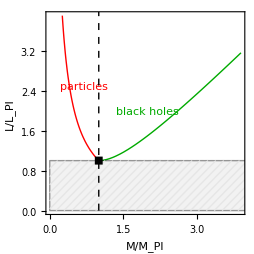

```mathematica
gupFakeHolo =Block[{xymax=4,β=1,γ=0,Y=2xB[#,β,γ]-1&},
shading = RegionPlot[y ≤ 1, {M,0,xymax},{y,0,xymax},
Mesh->30,MeshFunctions->{#1-#2&},MeshShading->{None},
MeshStyle->GrayLevel[0.9]];
Plot[ Evaluate[{
If[M≥ 1,Y[M],],
If[M≤ 1,1/M,]
}],
{M,0,xymax-0.1},PlotRange-> {0,xymax-0.1},
Frame-> True,
PlotStyle -> {
{Darker@Green},
{Red}
},
AspectRatio->1,
PlotRangePadding->None,
Prolog-> {
GrayLevel[.95],Rectangle[{0,0},{xymax,1}]
},
Epilog-> {
Black,square[{1,1},.08],
Dashed, Black,Line@{{1, 0},{1,xymax}},
Red,Text["particles", {0.7,2.5}],
Darker@Green, Text["black holes", {2,2}],
},
FrameLabel->  {"M/M_Pl", "L/L_Pl"},
ImageSize-> 9cm
]~Show~shading]
```

```mathematica
Export["../figures/completeness-gup-fake-holo.pdf", gupFakeHolo]
```

../figures/completeness-gup-fake-holo.pdf

```mathematica
(*GraphicsGrid[{{simpleSMM,gupFakeHolo}}]
Export["../figures/completeness-poster.pdf", %] *)
```

### Richtige GUP (auch für Thesis)

Hier versuch ich einfach Abbildung 6 aus Isi2013 nachzubauen, also d=4 Dimensionen.

```mathematica
MGUP[r_] = 1/2 r/Gamma[2, 0, r]
r0GUP = 1.45;
m0GUP = 2.42;
m0real = 1.67545; (* FindMinimum[MGUP[r],{r,2}] *)
r0real = 1.79328;
```

r/(2 Gamma[2,0,r])

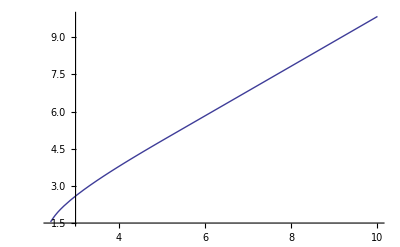

```mathematica
Plot[LGUPupper[x],{x,m0GUP,10}]
```

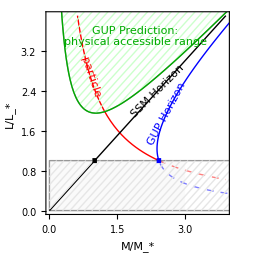

```mathematica
LGUPdata=Ninv[ MGUP[# r0GUP]  /MGUP[r0GUP]  m0GUP&, {0,5},{0,100}];
{LGUPupper,LGUPlower} = Interpolation[#@LGUPdata,InterpolationOrder->1]&/@{Select[#,#⟦2⟧>m0real&]&,Select[#,#⟦2⟧<m0real&]&};
(* Problem mit den LGU{upper,lower}: Der Grenzpunkt ist nicht so ganz klar bis wohin die gelten. Kaputte Kanten wo sie zusammenstossen! *)
particleGUPcurve[M_] := 1/M * m0GUP;
 realGUPfig =With[{β=1.9,γ=1, xymax=4},
Show[Plot[ Evaluate@{
If[M≤m0GUP,particleGUPcurve[M],],If[M≥ m0GUP,particleGUPcurve[M],],
If[M≤ 1 , M ,],If[M≥ 1, M ,],(*
If[M≥ r0real, LGUPupper[M] ,],
If[M≥ r0real,LGUPlower[M],]*)
},
{M,0,xymax-0.1},PlotRange-> {0,xymax-0.1},
Frame-> True,
PlotStyle -> {
{Red},
{Opacity[.5],Dashed, Red},
{Black},{Black},
{Blue},
{Thick, Opacity[.5],Dashed, Blue}
},
AspectRatio->1,
PlotRangePadding->None,
Prolog-> {
GrayLevel[.98],Rectangle[{0,0},{3,1}]
},
Epilog-> {
Black,square[{1,1},.05],
Blue,square[{m0GUP,1},.05],
Darker@Green, Text["GUP Prediction:\nphysical accessible range", {1.9,3.5}],
Red,EpiLabelsLoFrt[{0.9}, {particleGUPcurve}, {"particle"}],
Black,EpiLabelsLoFrt[{2.4}, {#&}, {"SSM Horizon"}],
Blue,EpiLabelsLoFrt[{2.6}, {LGUPupper}, {"GUP Horizon"}](*
EpiLabelsLoF[{1.5,2.2,2.4, 2.6,2.65,2.75},holoUpper,  {"n=0","n=1","n=2","n=3","n=4","..."}]*)
},
FrameLabel-> {"M/M_*", "L/L_*"}
],
ListLinePlot[Select[LGUPdata,#⟦2⟧>1&], PlotStyle-> {Blue}],
ListLinePlot[Select[LGUPdata,#⟦2⟧<1&],PlotStyle-> { Opacity[.5],Dashed, Blue}],
RegionPlot[y≥ xB[M,β,γ], {M,0,xymax},{y,0,xymax},
Mesh->20,MeshFunctions->{#1-#2&},MeshShading->{None},
MeshStyle->Lighter[Green,0.8]],
Plot[ xB[M,β,γ],{M,0,xymax},PlotStyle -> {Thick,Darker@Green}
],
RegionPlot[y ≤ 1, {M,0,xymax},{y,0,xymax},
Mesh->30,MeshFunctions->{#1-#2&},MeshShading->{None},
MeshStyle->GrayLevel[0.9]],
ImageSize-> 9cm
]
]
```

```mathematica
Export["../figures/completeness-real-gup.pdf", realGUPfig(*, ImageSize-> 8cm*)]
```

../figures/completeness-real-gup.pdf